```mathematica
<<myFunctionsMathematica8.m
```

{Temporary}

```mathematica
strm=OpenRead["2000 better zeros copy 2"];
zrs=ReadList[strm];
zero[n_]:=zrs[[n]]
```

```mathematica
bestzero[n_]:=1/2+I*t[n]
```

## n \mapsto t[n] is defined as a table in myFunctionsPureCodeV8 copy.nb, whhich is loaded by myFunctionsMathematica8.m. The table was created in my2ndEditOdlyzkoAccrtZrs6dec15.nb. It is from a table on Odlyzko’s site.

```mathematica
showData[data_]:=Print[Graphics[Raster[data]]]
```

```mathematica
pairToComplex[pair_]:=pair[[1]]+I*pair[[2]]
```

```mathematica
Map[pairToComplex,{{1,2},{3,4}}]
```

{1+2 ⅈ,3+4 ⅈ}

```mathematica
pairsetToComplexset[pairset_]:=Map[pairToComplex,pairset]
```

```mathematica
column[n_,matrix_]:=matrix[[All,n]]
```

```mathematica
mtrx={{1,2},{3,4},{5,6}};MatrixForm[mtrx]
```

(1 | 2
3 | 4
5 | 6)

```mathematica
column[1,%]
```

{1,3,5}

```mathematica
column[2,%%]
```

{2,4,6}

```mathematica
strm=OpenRead["zeros10^5odlyzko.txt"];
longzrs=ReadList[strm];
longzero[n_]:=.5+longzrs[[n]]*I
```

```mathematica
signsNoGraphics11[f_,center_,searchradius_,grain_,resolution_]:=
Module[{dta,row,shade,j,k,inc,m,w,seed,escape,green,white,blue,red,yellow,purple,aqua,black,orange,palegreen,u,v},
inc=searchradius/grain;
dta={};
black={0,0,0};
green={0,1,0};
blue={0,0,1};
red={1,0,0};
white={1,1,1};
yellow={1,1,0};
For[k=-searchradius-inc,k<searchradius,k=k+inc;
outk=k;
row={};
For[j=-searchradius-inc,j<searchradius,j=j+inc;
outj=j;
w=N[center+j+k*I];
u=Re[f[w]];
v=Im[f[w]];
shade=white;
If[Abs[u-.5]<resolution,shade=red];

row=Append[row,shade];

];
dta=Append[dta,row];
];

Return[dta]
]
```

```mathematica
signsNoGraphics10[f_,center_,searchradius_,grain_]:=
Module[{dta,row,shade,j,k,inc,m,w,seed,escape,green,white,blue,red,yellow,purple,aqua,black,orange,palegreen,u,v},
inc=searchradius/grain;
dta={};
black={0,0,0};
green={0,1,0};
blue={0,0,1};
red={1,0,0};
white={1,1,1};
yellow={1,1,0};
For[k=-searchradius-inc,k<searchradius,k=k+inc;
outk=k;
row={};
For[j=-searchradius-inc,j<searchradius,j=j+inc;
outj=j;
w=N[center+j+k*I];
u=Re[f[w]];
v=Im[f[w]];
shade=black;
If[u>0,If[v>0,shade=blue]];
If[u>0,If[Not[v>0],shade=green]];
If[u<0,If[v>0,shade=red]];
If[u<0,If[Not[v>0],shade=yellow]];


row=Append[row,shade];

];
dta=Append[dta,row];
];

Return[dta]
]
```

```mathematica
zeta1[z_]:=Module[{k,w,answer},
w=z;
For[k=0,k<1,k++;w=Zeta[w];
If[Abs[w]>10^8,Break[]];
If[Abs[w-1]<1/10^8,Break[]];

];
Return[w]];
z=0;
For[n=0,n<50,n++;z=N[zeta1[z]]];phi=z;
```

```mathematica
zetaIterate[s_,iteratenumber_]:=Module[{kk,w},
w=s;
For[kk=0,kk<iteratenumber,kk++;w=Zeta[w];
If[Abs[w]>10^10,Break[]]];
Return[w]
];
Attributes[zetaIterate]=Listable
```

Listable

```mathematica
phibasin[center_,searchradius_,lowbound_,grain_,escaperatio_,depth_]:=
Module[{row,shade,j,k,inc,m,n,w,seed,color,blue,green,yellow,red,white,black,dta,phi},
phi=0;For[n=0,n<50,n++;phi=N[Zeta[phi]]];
inc=searchradius/grain;
dta={};
black={0,0,0};
white={1,1,1};
green={0,1,0};
blue={0,0,1};
red={1,0,0};
yellow={1,1,0};
For[k=-searchradius-inc,k<searchradius,k=k+inc;
outk=k;
row={};
For[j=-searchradius-inc,j<searchradius,j=j+inc;
outj=j;
seed=N[center+j+k*I];
m=0;
w=seed;
color=white;
While[m<depth,m++;
outm=m;
w=N[Zeta[w]];
If[Abs[w-1]<lowbound*Abs[seed - 1],Break[]];
If[Abs[w]>escaperatio*Abs[seed],Break[]];
If[Abs[w-phi]<lowbound*Abs[seed - phi],color=black;Break[]]
];

row=Append[row,color]];
dta=Append[dta,row];
];


Return[dta]
]
```

```mathematica
arg[z_]:=Module[{answer},
answer=Arg[z];
If[Arg[z]<0,answer=Arg[z]+2*Pi];
Return[answer]];
Attributes[arg]=Listable
```

Listable

```mathematica
fOfCircleWindingNumberAroundZero4[f_,circlecenter_,radius_,grain_]:=
Module[{t,n,point,oldpoint,change,sumchange,theta,changedata,sumdata,argdata,thetalist,sign},

sumdata={};
changedata={};
sumchange=0;
point=f[circlecenter+radius];
thetalist={{0,arg[point]/(2*Pi)}};
For[n=0,n<grain  ,n++;
oldpoint=point;

point=f[circlecenter+radius*E^(2*Pi*I*n/grain)];
theta=arg[point]/(2*Pi);
theta=Min[theta,2-theta];

change=theta-Last[thetalist][[2]];
change=Mod[change,1];
If[change>.5,change=change-1];
thetalist=Append[thetalist,{n/grain,theta}];
changedata=Append[changedata,{n/grain,change}];
sumchange=sumchange+change;
sumdata=Append[sumdata,{n/grain,sumchange}]

];
Print["theta list"];
Print[ListPlot[thetalist,PlotStyle->Black]];
Print["change data"];
Print[ListPlot[changedata,PlotStyle->Red]];
Print["sum data"];
Print[ListPlot[sumdata,PlotStyle->Blue]];

Return[sumchange]
]
```

```mathematica
fOfCircleWindingNumberAroundZero5[f_,circlecenter_,radius_,grain_]:=
Module[{t,n,point,oldpoint,change,sumchange,theta,changedata,sumdata,argdata,thetalist,sign},

sumdata={};
changedata={};
sumchange=0;
point=f[circlecenter+radius];
thetalist={{0,arg[point]/(2*Pi)}};
For[n=0,n<grain  ,n++;
oldpoint=point;

point=f[circlecenter+radius*E^(2*Pi*I*n/grain)];
theta=arg[point]/(2*Pi);
theta=Min[theta,2-theta];

change=theta-Last[thetalist][[2]];
change=Mod[change,1];
If[change>.5,change=change-1];
thetalist=Append[thetalist,{n/grain,theta}];
changedata=Append[changedata,{n/grain,change}];
sumchange=sumchange+change;
sumdata=Append[sumdata,{n/grain,sumchange}]

];
Print["theta list"];
Print[ListPlot[thetalist,PlotStyle->Black]];
Print["change data"];
Print[ListPlot[changedata,PlotStyle->Red]];
Print["sum data"];
Print[ListPlot[sumdata,PlotStyle->Blue]];
Print["sum change   ",sumchange];
Return[sumchange]
];
```

```mathematica
minimize[f_,center_,range_,grain_]:=
Module[{best,j,k,inc,seed,start},
start=SessionTime[];
inc=range/grain;
best={center,f[center]};
For[k=-range/2-inc,k<range/2,k=k+inc;
kminimize=k;
row={};
For[j=-range/2-inc,j<range/2,j=j+inc;
jminimize=j;
seed=center+j+k*I;


If[f[seed]<best[[2]],best={seed,f[seed]}];

]
];
Return[best]

]
```

```mathematica
zeroFinder5[f_,startcenter_,startrange_,rangedivider_,grain_,depth_]:=
Module[{g,j,m,mz,s,best,oldmz,newrange,newcenter},
best={Infinity,Infinity};
g[s_]:=Abs[f[s]];
newrange=startrange;
newcenter=startcenter;
For[m=0,m<depth,m++;
outm=m;
mz=minimize[g,newcenter,newrange,grain];
If[Not[Abs[mz[[2]]]<best[[2]]],Return[best]];
If[Abs[mz[[2]]]<best[[2]],
best=mz;
newrange=newrange/rangedivider;
newcenter=best[[1]]]];
Return[best]]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

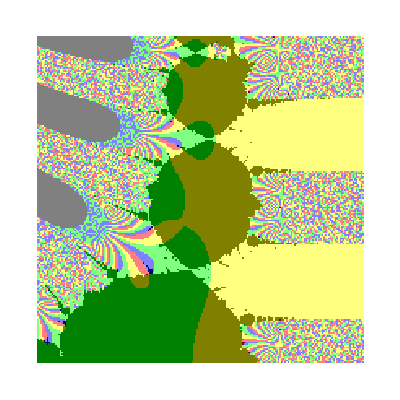

```mathematica
f[s_]:=zetaIterate[s,3]-s;
highbound=10^8;
lowbound=1/10^8;
center=zero[1];
searchradius=10;
grain=100;
escaperatio=10^15;
depth=100;
graydata=phibasin[center,searchradius,lowbound,grain,escaperatio,depth];
colordata=signsNoGraphics10[f,center,searchradius,grain];
showData[.5*(graydata+colordata)]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

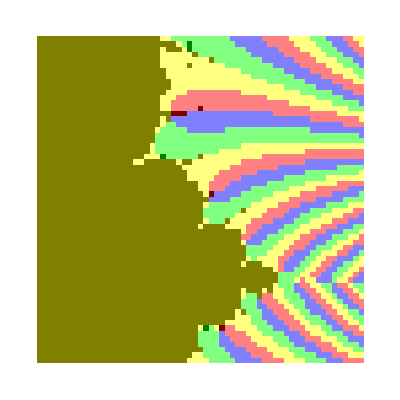

```mathematica
f[s_]:=zetaIterate[s,3]-s;
highbound=10^8;
lowbound=1/10^8;
center=zero[1]+3.4+.1*I;
searchradius=1;
grain=30;
escaperatio=10^15;
depth=100;
graydata=phibasin[center,searchradius,lowbound,grain,escaperatio,depth];
colordata=signsNoGraphics10[f,center,searchradius,grain];
showData[.5*(graydata+colordata)]
```

General::unfl: Underflow occurred in computation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

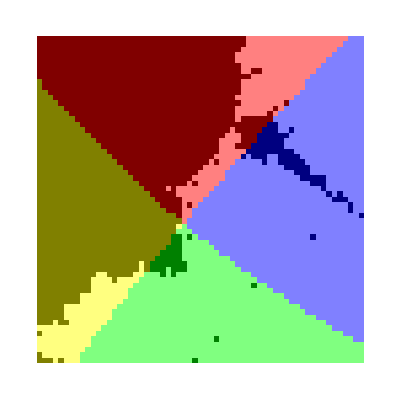

```mathematica
f[s_]:=zetaIterate[s,3]-s;
highbound=10^8;
lowbound=1/10^8;
center=zero[1]+3.46+.103*I;
searchradius=.01;
grain=30;
escaperatio=10^15;
depth=100;
graydata=phibasin[center,searchradius,lowbound,grain,escaperatio,depth];
colordata=signsNoGraphics10[f,center,searchradius,grain];
showData[.5*(graydata+colordata)]
```

```mathematica
stream=OpenWrite["rho1zeta3fixedpts13nfeb16"];
f[s_]:=zetaIterate[s,3]-s;
fixedpoints={};
startrange=2*searchradius;
rangedivider=2;
grain=20;
depth=20;
For[j=0,j<1,j++;
Print["_________________________________________________________________"];
startcenter=center;
fx=zeroFinder5[f,startcenter,startrange,rangedivider,grain,depth];
fxx=FindRoot[f[s],{s,fx[[1]]},WorkingPrecision->500][[1,2]];
Write[stream,fxx];
Print["fixed point imaginary part  "];
Print[Im[fxx]];
Print["fixed point real part  "];
Print[Re[fxx]];
Print["error"];
Print[f[fxx]];
Print["distance from Riemann zero"];
Print[Abs[fxx-zero[j]]]];
Close[stream]
```

_________________________________________________________________

fixed point imaginary part

14.236228563221813322871223010855881692998712362084943995686954378256069322896396761526007136189745757467102551375667154010366364994538731791627111382325375111094897277576221794166383077071426204175566403532396710787895292044043947643155315825880513523093272920043436541351728207780017861238006999109644383198471665302823015355865202971277187847669197416821841529316526704660632740545865576528002773249512580215052792457282410834191507107658393848458313664113623935800293262678700791600125465010766853

fixed point real part

3.9589623348847434673516458439896123461477039951866801455882506555054331235719797619129160432526832126428515417856326242408422124490775895372199766744584091417426621757010890812527273950737143989685323563781225513830208463414952467080996514470354165736042850223082013542860938536894453944241116438492746243199878001238993540770158034816978947866042863811536518002674033394246742728451523022955079328623947833520567532298244004442294156837342370982002330874074322076777185746207730323482406094614280046

error

0.+0. ⅈ

distance from Riemann zero

3.46045

rho1zeta3fixedpts13nfeb16

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

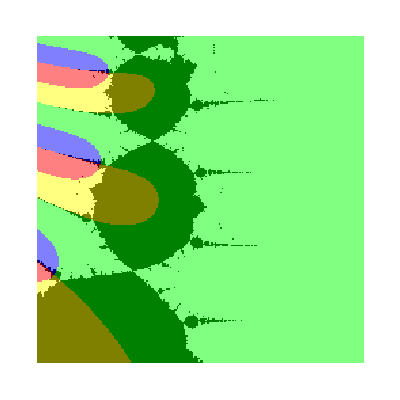

```mathematica
f[s_]:=zetaIterate[s,1]-bestzero[1];
highbound=10^8;
lowbound=1/10^8;
center=fxx;
searchradius=10;
grain=120;
escaperatio=10^15;
depth=100;
graydata=phibasin[center,searchradius,lowbound,grain,escaperatio,depth];
colordata=signsNoGraphics10[f,center,searchradius,grain];
showData[.5*(graydata+colordata)]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

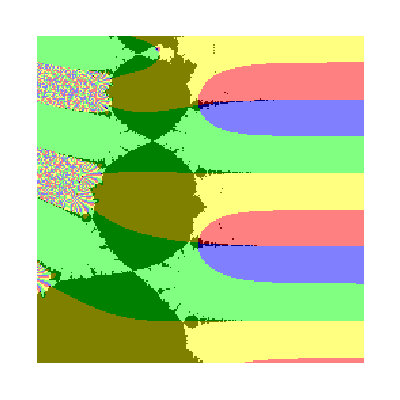

```mathematica
f[s_]:=zetaIterate[s,2]-bestzero[1];
highbound=10^8;
lowbound=1/10^8;
center=fxx;
searchradius=10;
grain=120;
escaperatio=10^15;
depth=100;
graydata=phibasin[center,searchradius,lowbound,grain,escaperatio,depth];
colordata=signsNoGraphics10[f,center,searchradius,grain];
showData[.5*(graydata+colordata)]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

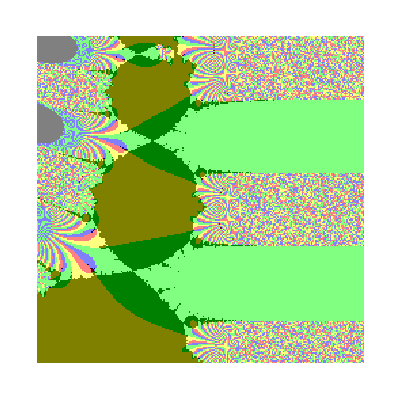

```mathematica
f[s_]:=zetaIterate[s,3]-bestzero[1];
highbound=10^8;
lowbound=1/10^8;
center=fxx;
searchradius=10;
grain=120;
escaperatio=10^15;
depth=100;
graydata=phibasin[center,searchradius,lowbound,grain,escaperatio,depth];
colordata=signsNoGraphics10[f,center,searchradius,grain];
showData[.5*(graydata+colordata)]
```

```mathematica
streem=OpenWrite["zeta3backorbit8mar16"];
zeros={bestzero[1]};
For[k=1,k<200,k++;
startcenter=fxx;
x=zeros[[k-1]];
zr=FindRoot[zetaIterate[s,3]-x,{s,startcenter},PrecisionGoal->300,WorkingPrecision->495][[1,2]];
zeros=Append[zeros,zr];
Write[streem,{k,zr}]];
Close[streem]
```

zeta3backorbit8mar16

```mathematica
lz=Last[zeros]
```

3.9589623348847434673516458439896123461477039951866801455882506555054331235719797619129160432526832126428515417856326242408422124490775895372199766744584091417426621757010890812527273950737143989685323563781225513830208463414952467080996514470354165736042850223082013542860938536894453944241116438492746243199878001238993540770158034816978947866042863811536518002674033394246742728451523022955079328623947833520567532298244004442294156837342370982002330874074322076786546987552331235839008381897+14.2362285632218133228712230108558816929987123620849439956869543782560693228963967615260071361897457574671025513756671540103663649945387317916271113823253751110948972775762217941663830770714262041755664035323967107878952920440439476431553158258805135230932729200434365413517282077800178612380069991096443831984716653028230153558652029712771878476691974168218415293165267046606327405458655765280027732495125802150527924572824108341915071076583938484583136641136239357875444170882720385455648254869 ⅈ

```mathematica
zetaIterate[zeros[[2]],3]-bestzero[1]
```

0.+0. ⅈ

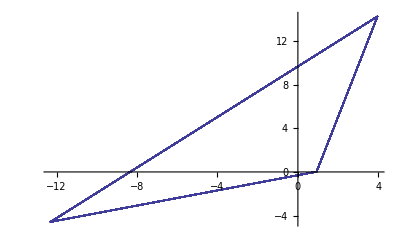

```mathematica
w=lz;
pairs={{Re[w],Im[w]}};
For[n=0,n<200,n++;
w=Zeta[w];
pair={Re[w],Im[w]};
pairs=Append[pairs,pair]];
ListPlot[pairs,Joined->True]
```

```mathematica
fxx=3.9589623348847434673516458439896123461477039951866801455882506555054331235719797619129160432526832126428515417856326242408422124490775895372199766744584091417426621757010890812527273950737143989685323563781225513830208463414952467080996514470354165736042850223082013542860938536894453944241116438492746243199878001238993540770158034816978947866042863811536518002674033394246742728451523022955079328623947833520567532298244004442294156837342370982002330874074322076777185746207730323482406094614280045560001275620833890525`500.+I*14.2362285632218133228712230108558816929987123620849439956869543782560693228963967615260071361897457574671025513756671540103663649945387317916271113823253751110948972775762217941663830770714262041755664035323967107878952920440439476431553158258805135230932729200434365413517282077800178612380069991096443831984716653028230153558652029712771878476691974168218415293165267046606327405458655765280027732495125802150527924572824108341915071076583938484583136641136239358002932626787007916001254650107668531722108762729843632444`500.
```

3.9589623348847434673516458439896123461477039951866801455882506555054331235719797619129160432526832126428515417856326242408422124490775895372199766744584091417426621757010890812527273950737143989685323563781225513830208463414952467080996514470354165736042850223082013542860938536894453944241116438492746243199878001238993540770158034816978947866042863811536518002674033394246742728451523022955079328623947833520567532298244004442294156837342370982002330874074322076777185746207730323482406094614280046+14.236228563221813322871223010855881692998712362084943995686954378256069322896396761526007136189745757467102551375667154010366364994538731791627111382325375111094897277576221794166383077071426204175566403532396710787895292044043947643155315825880513523093272920043436541351728207780017861238006999109644383198471665302823015355865202971277187847669197416821841529316526704660632740545865576528002773249512580215052792457282410834191507107658393848458313664113623935800293262678700791600125465010766853 ⅈ

```mathematica
streem=OpenRead["zeta3backorbit8mar16"];
list=ReadList[streem];
Close[streem]
```

zeta3backorbit8mar16

```mathematica
Length[list]
```

199

```mathematica
list0={};
list1={};
list2={};
For[n=0,n<199,
n++;
list0=Append[list0,list[[n,2]]];
list1=Append[list1,Zeta[list[[n,2]]]];
list2=Append[list2,Zeta[Zeta[list[[n,2]]]]]];
```

```mathematica
Length[list2]
```

199

## Here I map the zeta^{circ 3} backorbit of fxx by zeta twice and plot the three sets against fxx and its two images. Below, I’ll map the forward zeta orbit of the deepest member of the original backward orbit, to verify that I get the same backward orbit of rho_1.

```mathematica
pairs0={};
pairs1={};
pairs2={};
For[n=0,n<199,n++;
zr=list0[[n]];
la=Re[Log[Abs[zr-fxx]]];
theta=Arg[zr-fxx];
pair={la*Cos[theta],la*Sin[theta]};
pairs0=Append[pairs0,pair];
zr=list1[[n]];
la=Re[Log[Abs[zr-Zeta[fxx]]]];
theta=Arg[zr-Zeta[fxx]];
pair={la*Cos[theta],la*Sin[theta]};
pairs1=Append[pairs1,pair];
zr=list2[[n]];
la=Re[Log[Abs[zr-Zeta[Zeta[fxx]]]]];
theta=Arg[zr-Zeta[Zeta[fxx]]];
pair={la*Cos[theta],la*Sin[theta]};
pairs2=Append[pairs2,pair]]
```

```mathematica
Length[pairs0]
```

199

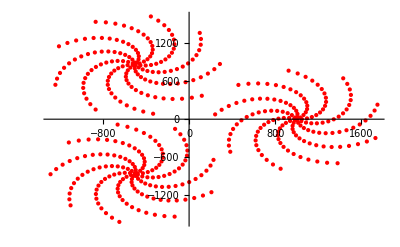

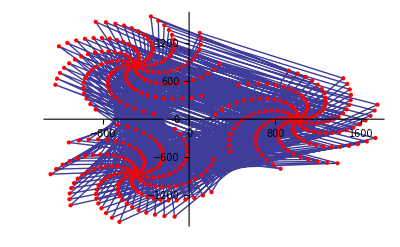

```mathematica
center0={1000,0};
center1={1000*Cos[2*Pi/3],1000*Sin[2*Pi/3]};
center2={1000*Cos[4*Pi/3],1000*Sin[4*Pi/3]};
pairs={};
For[n=0,n<150,n++;
pair1=pairs0[[n]]+center0;
pairs=Append[pairs,pair1];
pair2=pairs1[[n]]+center1;
pairs=Append[pairs,pair2];
pair3=pairs2[[n]]+center2;
pairs=Append[pairs,pair3]];
p1=ListPlot[pairs,Joined->True];
p2=ListPlot[pairs,PlotStyle->Red];
Print[p2];
Show[p1,p2]
```

```mathematica
list[[1,2]]
```

3.94714051388596561408389641946529075389002954628822898216160558012484824168220212563205370316901104484345786223608083932854034246421818446729434389130667705767735629123410962283127579054522530760938401202146868254294572840718079986177248218539678525103827449995624478720405890389486280100794822585914841489421469207478658704826846104301523278690189739142071977165746520104470715827015797434313838464605502952101720151387254611878473859407907435646567644105400120333506842768543625850760832083812+14.2478417061144484856730770081359036305256096825002456609130425712351888530763718624675068221463504198067422119255817134675246203581388882018052105999515889349061356723886012921895649890370012481573330440708318798316663694793985778283235058094413513054808369282616011572530549736844810723909056068579067589791157870637115730018737882574406684046853756726548454372614345538960570797599635457925301591711840328934140179203492488396707875305254784788607365764146222236214740881469244727584134450135 ⅈ

```mathematica
zetaIterate[list[[1,2]],3]-bestzero[1]
```

0.+0. ⅈ

```mathematica
zetaIterate[list[[2,2]],6]-bestzero[1]
```

0.+0. ⅈ

```mathematica
zetaIterate[list[[110,2]],3*110]-bestzero[1]
```

0.+0. ⅈ

```mathematica
zetaIterate[list[[113,2]],3*113]-bestzero[1]
```

0.+0. ⅈ

```mathematica
zetaIterate[list[[100,2]],3*100]-bestzero[1]
```

0.+0. ⅈ

```mathematica
list[70,2]
```

```mathematica
fxx0=fxx;
fxx1=Zeta[fxx0];
fxx2=Zeta[fxx1];
z0=list[[113,2]];
forward0={z0-fxx0};
forward1={};
forward2={};
For[n=0,n<113,n++;
z1=Zeta[z0];
z2=Zeta[z1];
forward0=Append[forward0,z0-fxx0];
forward1=Append[forward1,z1-fxx1];
forward2=Append[forward2,z2-fxx2];
z0=Zeta[z2]];
{Length[forward0],Length[forward1],Length[forward2]}
```

{114,113,113}

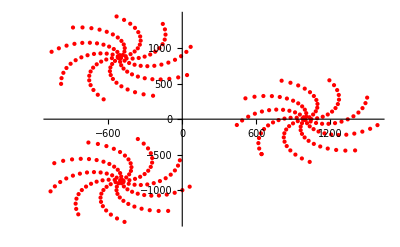

```mathematica
center0={1000,0};
center1={1000*Cos[2*Pi/3],1000*Sin[2*Pi/3]};
center2={1000*Cos[4*Pi/3],1000*Sin[4*Pi/3]};
pairs={};

For[n=0,n<113,n++;
la=Re[Log[Abs[forward0[[n]]]]];
arg=Arg[forward0[[n]]];
pair={la*Cos[arg],la*Sin[arg]}+center0;
pairs=Append[pairs,pair];

la=Re[Log[Abs[forward1[[n]]]]];
arg=Arg[forward1[[n]]];
pair={la*Cos[arg],la*Sin[arg]}+center1;
pairs=Append[pairs,pair];

la=Re[Log[Abs[forward2[[n]]]]];
arg=Arg[forward2[[n]]];
pair={la*Cos[arg],la*Sin[arg]}+center2;
pairs=Append[pairs,pair]];
p1=ListPlot[pairs,Joined->True];
p2=ListPlot[pairs,PlotStyle->Red];
Print[p2];
Show[p1,p2]
```

## leaf5point9r2c2

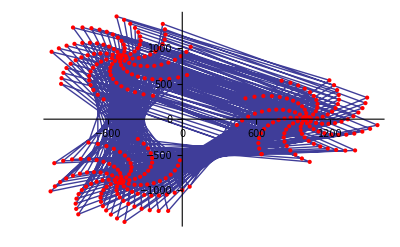

```mathematica
Length[pairs]
```

339

```mathematica
pairs0={};
pairs1={};
pairs2={};
For[n=0,n<339,n++;
If[Mod[n,3]==1,pairs0=Append[pairs0,pairs[[n]]]];
If[Mod[n,3]==2,pairs1=Append[pairs1,pairs[[n]]]];
If[Mod[n,3]==0,pairs2=Append[pairs2,pairs[[n]]]]];
p0=ListPlot[pairs0,PlotStyle->{Red,PointSize[.015]}];
p1=ListPlot[pairs1,PlotStyle->{Red,PointSize[.015]}];
p2=ListPlot[pairs2,PlotStyle->{Red,PointSize[.015]}];
p0j=ListPlot[pairs0,Joined->True];
p1j=ListPlot[pairs1,Joined->True];
p2j=ListPlot[pairs2,Joined->True];
Print[Show[p0,p0j]];
Print[Show[p1,p1j]];
Print[Show[p2,p2j]];
```

## leaf5oint9r1c1

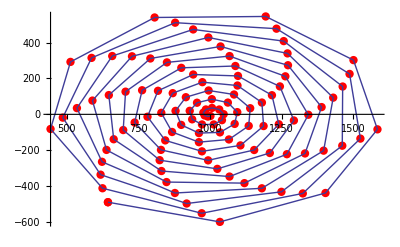

## leaf5point9r1c2

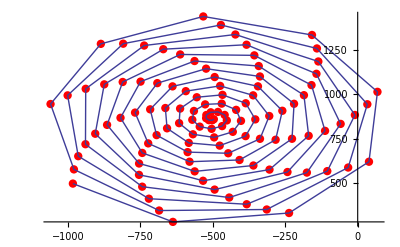

## leaf5point9r2c1